```mathematica
ψ[r_,z_,v_,a_]=-1/2 v r^2(1-3/2 a/((r^2+z^2)^(1/2))+1/2(a/((r^2+z^2)^(1/2)))^3);

vz[r_,z_,v_,a_]=1/r D[ψ[r,z,v],r]
vr[r_,z_,v_,a_]=-1/r D[ψ[r,z,v],z]
```

(-1/2 r^2 v (-(3 a^3 r)/(2 (r^2+z^2)^(5/2))+(3 a r)/(2 (r^2+z^2)^(3/2)))-r v (1+a^3/(2 (r^2+z^2)^(3/2))-(3 a)/(2 √(r^2+z^2))))/r

1/2 r v (-(3 a^3 z)/(2 (r^2+z^2)^(5/2))+(3 a z)/(2 (r^2+z^2)^(3/2)))

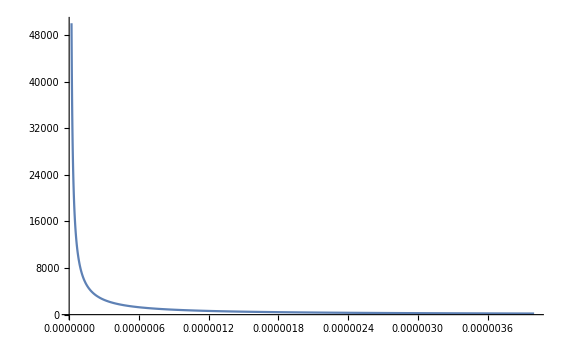

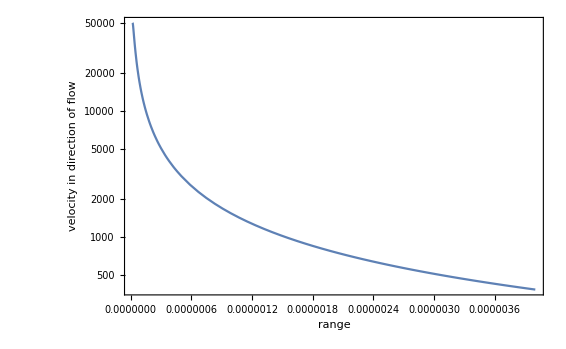

```mathematica
Plot[{vz[r,0,vel,rad]+vel},{r,rad,domain},AxesOrigin->{0,0},PlotRange->All]
LogPlot[{vz[rad/100,z,vel,rad]+vel},{z,rad,domain},AxesOrigin->{0,0},PlotRange->All,Frame->True,FrameLabel->{"range","velocity in direction of flow"}]
```

```mathematica
domain=0.4*10^-5;
cells=256;
dx=domain/cells;
rad=1.3*dx
vel=50000;
```

2.03125×10^-8

```mathematica
dt
```

```mathematica
Limit[Simplify[(-1/2 r^2 v (-(3 a^3 r)/(2 (r^2+z^2)^(5/2))+(3 a r)/(2 (r^2+z^2)^(3/2)))-r v (1+a^3/(2 (r^2+z^2)^(3/2))-(3 a)/(2 √(r^2+z^2))))/r],r->0]
```

-(v (a^3-3 a z^2+2 (z^2)^(3/2)))/(2 (z^2)^(3/2))